```mathematica
Solve[(({{-s0 Γ1, Γ1+s0 Γ1}, {s0 Γ1, -Γ1 + s0 Γ1}}).{Ng, Ne}==0 )&& (Ng + Ne ==  1), {Ng, Ne}]
```

{{Ng→1-s0,Ne→s0}}

```mathematica
M = ({{-α1-α2-α3, β1+α1, β2+α2, β3+α3}, {α1, -β1 - α1, 0, 0}, {α2, 0, -β2-α2, 0}, {α3, 0, 0, -β3 - α3}});
```

```mathematica
{s, j} = JordanDecomposition[M];
```

```mathematica
s// MatrixForm
```

((-α2+β2)/α2 | (-2 α2-β1+β2-√(4 α1 α2+β1^2-2 β1 β2+β2^2))/(2 α2) | (-2 α2-β1+β2+√(4 α1 α2+β1^2-2 β1 β2+β2^2))/(2 α2)
(α1 (α2-β2))/(α2 (α1-β1)) | (β1-β2+√(4 α1 α2+β1^2-2 β1 β2+β2^2))/(2 α2) | (β1-β2-√(4 α1 α2+β1^2-2 β1 β2+β2^2))/(2 α2)
1 | 1 | 1)

```mathematica
M
```

{{-α1-α2-α3,-α1+β1,-α2+β2,-α3+β3},{α1,α1-β1,0,0},{α2,0,α2-β2,0},{α3,0,0,α3-β3}}

```mathematica
sol = Solve[M.{N0, N1, N2, N3} == {0,0,0, 0} && N0 + N1 + N2 + N3 == Ν, {N0, N1, N2, N3}]⟦1⟧
```

{N0→-((α1-β1) (α2-β2) (α3-β3) Ν)/(2 α1 α2 α3-α2 α3 β1-α1 α3 β2-α1 α2 β3+β1 β2 β3),N1→(α1 (α2-β2) (α3-β3) Ν)/(2 α1 α2 α3-α2 α3 β1-α1 α3 β2-α1 α2 β3+β1 β2 β3),N2→(α2 (α1-β1) (α3-β3) Ν)/(2 α1 α2 α3-α2 α3 β1-α1 α3 β2-α1 α2 β3+β1 β2 β3),N3→((α1 α2 α3-α2 α3 β1-α1 α3 β2+α3 β1 β2) Ν)/(2 α1 α2 α3-α2 α3 β1-α1 α3 β2-α1 α2 β3+β1 β2 β3)}

```mathematica
Limit[{N0, N1, N2, N3} /.sol, {β1 -> Γ0, β2 -> 0, β3 -> 0, α1 -> (s0 Γ0)/2, α2 -> 0,α3 -> 0, Ν -> 1} ]
```

{1-s0/2,s0/2,0,0}

```mathematica
sol = Solve[M.{N0, N1, N2, N3} == {0,0,0, 0} && N0 + N1 + N2 + N3 == Ν, {N0, N1, N2, N3}]⟦1⟧ /. {β1 -> Γ0, β2 -> Γ0, β3 -> Γ0, α1 -> (s0 Γ0)/2, α2 -> (s0 Γ0)/2,α3 -> (s0 Γ0)/2, Ν -> 1} // FullSimplify
```

{N0→(2-s0)/(2+2 s0),N1→s0/(2+2 s0),N2→s0/(2+2 s0),N3→s0/(2+2 s0)}

```mathematica
((N0 - N1 )/. sol )// FullSimplify
```

-1+2/(1+s0)

```mathematica
{N0, N1, N2, N3} /. sol
```

{(2-s0)/(2+2 s0),s0/(2+2 s0),s0/(2+2 s0),s0/(2+2 s0)}

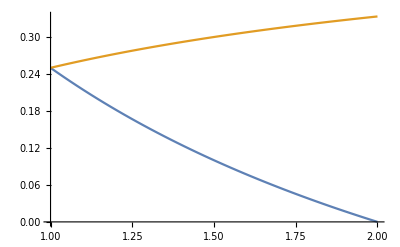

```mathematica
Plot[{(2-s0)/(2+2 s0),s0/(2+2 s0)}, {s0, 1, 2}]
```